## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "Parameters.m", "Cache.m","aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

## Определения

### Система координат

```mathematica
Spher;
RecalculateGrav[];
```

### Базовые определения

#### Константы

```mathematica
l1=l(l+1)/2;
l2=(l-1)(l+2);
l3=l1 l2 / 2;
```

```mathematica
sql2=√l2;
```

#### Тензоры

```mathematica
thmask[Odd]=<|12->0,Even->0,Odd->0,13->1,23->1|>;
thmask[Even]=<|12->1,Even->1,Odd->1,13->0,23->0|>;

thmasked[m_][th_Association]:=th thmask[m];

metr={{1/r,1,Sin[u]},{1,r ,r Sin[u]},{Sin[u],r Sin[u],r Sin[u]^2}};

tha=<|KeyValueMap[(#1->(f[#1])#2)&,<|
12->LegendreP[l,1,Cos[u]],
Even->LegendreP[l,Cos[u]],
Odd->LegendreP[l,2,Cos[u]],
13->LegendreP[l,1,Cos[u]],
23->LegendreP[l,2,Cos[u]]
|>]|>;

MakeTensor[th_Association]:=metr{{-2th[Even],th[12],th[13]},{th[12],th[Even]+th[Odd],th[23]},{th[13],th[23],th[Even]-th[Odd]}};
MakeTensor[m_][th_Association]:=MakeTensor[th//thmasked[m]];
```

#### Решения

```mathematica
sln[Generic][f[11]]=-2sln[Generic][f[Even]];
```

```mathematica
sln[Generic][f[13]]=SphericalHankelH1[l,r ω];
sln[Generic][f[23]]=-(-2 f[r]-r f'[r])/((-1+l) (2+l))/.{f->(sln[Generic][f[13]]/.r->#&)}//FullSimplify;
```

```mathematica
sln[Generic][f[Even]]=sln[Generic][f[13]]/r/.{C[1]->C[3],C[2]->C[4]};
sln[Generic][f[Odd]]=-((4+l+l^2-2 r^2 ω^2) f[r]+2 r f'[r])/((-1+l) l (1+l) (2+l))/.{f->(sln[Generic][f[Even]]/.r->#&)}//FullSimplify;
sln[Generic][f[12]]=-(4 f[r]+2 r f'[r])/(l+l^2)/.{f->(sln[Generic][f[Even]]/.r->#&)}//FullSimplify;
```

```mathematica
sln[zone__][eo:Even|Odd|All]:=Evaluate@(thmasked[eo][tha])/.{x:f[__]:>sln[zone][x]};
```

#### Операторы повышения и понижения

```mathematica
up[Scalar,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f);
up[Vector,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f+sgn Csc[u]{{0,-I},{I,0}}.f );
up[Tensor,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f+2 sgn Csc[u]{{0,-I},{I,0}}.f);
```

```mathematica
up[All,sgn_:+1][th_,m_]:=Module[{thu=th},
thu[Even]=up[Scalar,sgn][#,m]&@th[Even];
{thu[12],thu[13]}=up[Vector,sgn][#,m]&@{th[12],th[13]};
{thu[23],thu[Odd]}=up[Tensor,sgn][#,m]&@{th[23],th[Odd]};
thu//Simplify
];
```

#### Функции

```mathematica
TensorNormRe[th_]:=Sum[hh[i,k]hh[j,l]Re[th[[i,j]]]Re[th[[k,l]]],{i,3},{j,3},{k,3},{l,3}];
```

#### Инварианты и соотношения

```mathematica
eq[sdivh][th_]:=Module[{i,j,k},Table[Sum[hh[j,k]ddd[th,i,j,k],{j,3},{k,3}],{i,3}]];
```

### Решатели и отображатели

#### Обобщенные табуляторы

```mathematica
series[zone__][eo__][{n_Integer}]:=Module[{l0},Table[series[zone][eo][l0],{l0,2,n}]];
series[zone__][eo__][l0_Integer]:=Module[{m,s,sl},
Block[{l=l0},
s=sln[zone][eo]//Normal//FunctionExpand//Simplify//PowerExpand//Simplify//Association;
sl={s};
Do[AppendTo[sl,s=up[All][s,m-1]],{m,1,l0}];
];
sl
];
```

```mathematica
intern[zone__][eo__][series][n_Integer,cfg_List:{energy,pointing,TensorNormRe}]:=Module[{},
Cache[cache[zone][eo][series]=series[zone][eo][{n}],
Length[#]+1<n&];
Cache[cache[zone][eo][series,Tensor]=Table[j Exp[-I ω ct]//MakeTensor[#]&,{i,cache[zone][eo][series]},{j,i}],
Length[#]+1<n&];
If[MemberQ[cfg,energy],
Cache[cache[zone][eo][series,energy]=
Table[EvaluateAt[epsnem,{th[a_,b_]:>j[[a,b]]}],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing],
Cache[cache[zone][eo][series,pointing]=
Table[EvaluateAt[Uinem,{th[a_,b_]:>j[[a,b]]}],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,TensorNormRe],
Cache[cache[zone][eo][series,TensorNormRe]=
Table[TensorNormRe[j]//Simplify,{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
];
```

#### Плоттинг

```mathematica
splt[angle][f_,o:OptionsPattern[]]:=SphericalPlot3D[f/.{ω->1,ct->0},{u,0,π},{w,0,2π},o];
```

```mathematica
plt[radial][f_,range_,o:OptionsPattern[]]:=Plot[f,{r}~Join~range//Evaluate,o];
```

```mathematica
denplt[energy][f_,range_,o:OptionsPattern[]]:=Module[{x,y,f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=f0/.{r->√(x^2+y^2),u->ArcTan[x/√(x^2+y^2),y/√(x^2+y^2)]}},
DensityPlot[Log[Abs[f1]+1],{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o]//Quiet
]];
```

```mathematica
plt3d[energy][f_,range_,o:OptionsPattern[]]:=Module[{x,y,f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=f0/.{r->√(x^2+y^2),u->ArcTan[x/√(x^2+y^2),y/√(x^2+y^2)]}},
Plot3D[f1,{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o]//Quiet
]];
```

```mathematica
denplt[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{x,y,f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=f0/.{r->√(x^2+y^2),u->ArcTan[x/√(x^2+y^2),y/√(x^2+y^2)]}},DensityPlot[Log[Abs[(f1)[[i]]]+1],{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
denplt[pointing,i_List][f_,range_,o:OptionsPattern[]]:=denplt[pointing,#][f,range,o]&/@i;
```

```mathematica
plt3d[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{x,y,f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=f0/.{r->√(x^2+y^2),u->ArcTan[x/√(x^2+y^2),y/√(x^2+y^2)]}},Plot3D[(f1)[[i]],{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
plt3d[pointing,i_List][f_,range_,o:OptionsPattern[]]:=plt3d[pointing,#][f,range,o]&/@i;
```

## Волны общего вида

### Угловые части

```mathematica
intern[Generic][Odd][series][5,{TensorNormRe}];
intern[Generic][Even][series][5,{TensorNormRe}];
```

```mathematica
cache[Generic][Odd][angle,splt]=With[{lm={{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{2,4}}},
{({#[[1]]+1,#[[2]]-1}&)/@lm}~Join~Table[splt[angle][#, PlotRange->Full]&/@(cache[Generic][Odd][series,TensorNormRe][[Sequence@@#]]&/@lm)//Parallelize,{r,{0.1,2,4,6,10,100}}]
];
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Generic][Even][angle,splt]=With[{lm={{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{2,4}}},
{({#[[1]]+1,#[[2]]-1}&)/@lm}~Join~Table[splt[angle][#, PlotRange->Full]&/@(cache[Generic][Even][series,TensorNormRe][[Sequence@@#]]&/@lm)//Parallelize,{r,{0.1,2,4,6,10,100}}]
];
%//Grid//Rasterize
```

-Graphics-

### Радиальные части

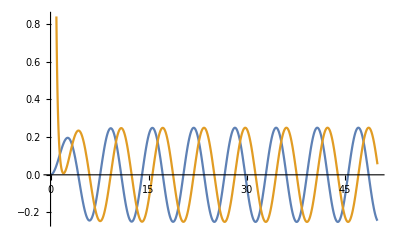
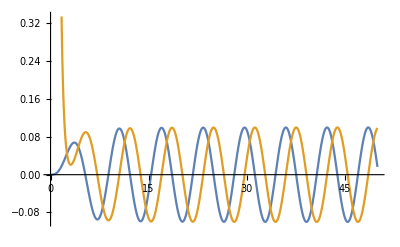
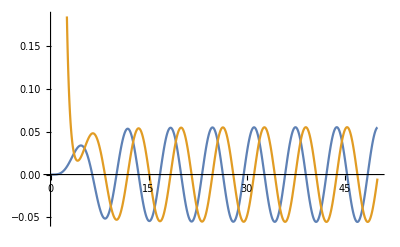
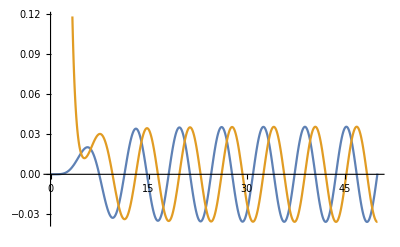
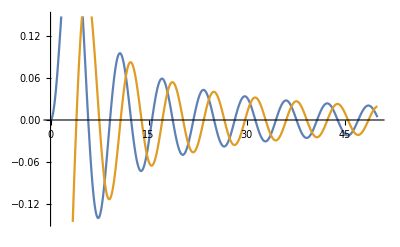
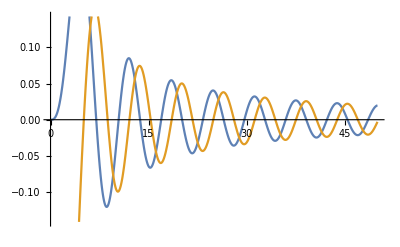
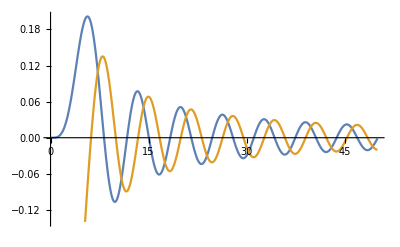
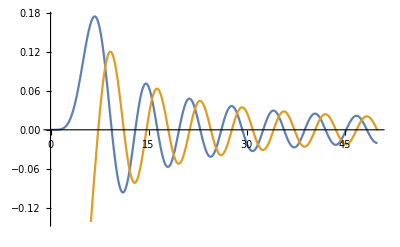
f23 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f13 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fe | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fo | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f12 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
{"f23"}~Join~Table[plt[radial][sln[Generic][f[23]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"f13"}~Join~Table[plt[radial][sln[Generic][f[13]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"fe"}~Join~Table[plt[radial][sln[Generic][f[Even]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"fo"}~Join~Table[plt[radial][sln[Generic][f[Odd]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"f12"}~Join~Table[plt[radial][sln[Generic][f[12]]/.{ω->1}//ReIm,{0,50}],{l,2,5}]
},Frame->All]
```

### Плотность и поток энергии

#### Нечетные моды

```mathematica
intern[Generic][Odd][series][3];
```

```mathematica
cache[Generic][Odd][energy,plt3d]={plt3d[energy][#,{-5,5},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Generic][Odd][energy,denplt]={denplt[energy][#,{-5,5},MaxRecursion->0,PlotPoints->100]&/@(cache[Generic][Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Generic][Odd][pointing,plt3d]={plt3d[pointing,{1,2,3}][#,{-5,5},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Generic][Odd][pointing,denplt]={denplt[pointing,{1,2,3}][#,{-5,5},MaxRecursion->0,PlotPoints->100]&/@(cache[Generic][Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

#### Четные моды

```mathematica
intern[Generic][Even][series][3];
```

```mathematica
cache[Generic][Even][energy,plt3d]={plt3d[energy][#,{-5,5},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Even][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Generic][Even][energy,denplt]={denplt[energy][#,{-5,5},MaxRecursion->0,PlotPoints->100]&/@(cache[Generic][Even][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Generic][Even][pointing,plt3d]={plt3d[pointing,{1,2,3}][#,{-5,5},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Even][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Generic][Even][pointing,denplt]={denplt[pointing,{1,2,3}][#,{-5,5},MaxRecursion->0,PlotPoints->100]&/@(cache[Generic][Even][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

### Различные соотношения

```mathematica
intern[Generic][Odd][series][5,{}]
```

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify//Chop
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify//Chop
```

{{{0.0502331-0.0940001 ⅈ,0.304547+0.0625999 ⅈ,0.106516-0.518199 ⅈ},{0.534522+0.210635 ⅈ,-0.100914+0.21835 ⅈ,1.57308+0.727028 ⅈ}},{{0.0458035-0.0306731 ⅈ,0.200866+0.178604 ⅈ,0.303902-0.341781 ⅈ},{0.204916+0.170006 ⅈ,-0.121707+0.202953 ⅈ,1.46215+0.876828 ⅈ}},{{0.0323082-0.00166683 ⅈ,0.0632049+0.225448 ⅈ,0.383608-0.107546 ⅈ},{0.0666971+0.131447 ⅈ,-0.175851+0.134521 ⅈ,0.969143+1.2669 ⅈ}},{{0.0179491+0.0102291 ⅈ,-0.0654644+0.195807 ⅈ,0.333173+0.11139 ⅈ},{-0.000219216+0.0910439 ⅈ,-0.199657+0.0354797 ⅈ,0.25561+1.43841 ⅈ}}}

```mathematica
intern[Generic][Even][series][5,{}]
```

```mathematica
eq[sdivh][cache[Generic][Even][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify//Chop
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
eq[sdivh][cache[Generic][Even][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify//Chop
```

{{{0.0120794-0.00137584 ⅈ,0.0899163-0.0654326 ⅈ,0.0159767+0.0159854 ⅈ},{-0.0131477+0.0514923 ⅈ,-0.24661+0.340824 ⅈ,-0.14655+0.0256232 ⅈ}},{{0.00675947+0.00195676 ⅈ,0.116138-0.0465498 ⅈ,0.00633779+0.0156899 ⅈ},{-0.00428694+0.0269158 ⅈ,0.0433212+0.355779 ⅈ,-0.0773669-0.00228577 ⅈ}},{{0.00314058+0.00311358 ⅈ,0.122659+0.0114246 ⅈ,-0.00152341+0.01363 ⅈ},{-0.00679349+0.0160979 ⅈ,-0.00346068+0.400507 ⅈ,-0.0467572-0.0161838 ⅈ}},{{0.000698502+0.00286479 ⅈ,0.0930753+0.0693119 ⅈ,-0.0071065+0.00916934 ⅈ},{-0.00858082+0.00831792 ⅈ,-0.154801+0.372786 ⅈ,-0.0269852-0.0235636 ⅈ}}}

### Черновик